Question 1

Cost function is TC(Q)=3072+1856 Q-180 Q^2+6 Q^3

Q_min^AVC=15

Q_min^MC=10

Q_min^ATC=16

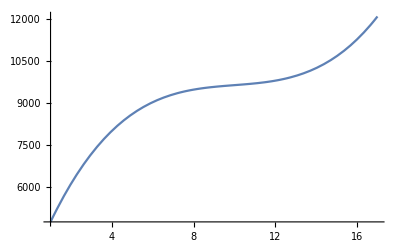

Question 2

Cost function is TC(Q)=980+693 Q-120 Q^2+10 Q^3

Q_min^AVC=6

Q_min^MC=4

Q_min^ATC=7

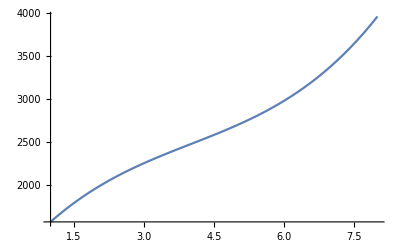

Question 3

Cost function is TC(Q)=14450+1280 Q-120 Q^2+5 Q^3

Q_min^AVC=12

Q_min^MC=8

Q_min^ATC=17

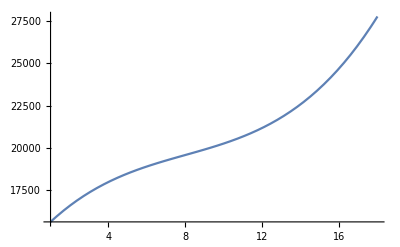

Question 4

Cost function is TC(Q)=15680+1643 Q-144 Q^2+8 Q^3

Q_min^AVC=9

Q_min^MC=6

Q_min^ATC=14

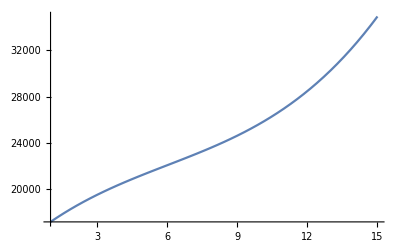

Question 5

Cost function is TC(Q)=32+12 Q-6 Q^2+Q^3

Q_min^AVC=3

Q_min^MC=2

Q_min^ATC=4

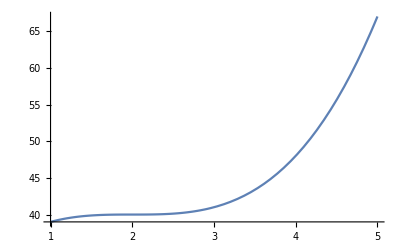

Question 6

Cost function is TC(Q)=484+255 Q-18 Q^2+Q^3

Q_min^AVC=9

Q_min^MC=6

Q_min^ATC=11

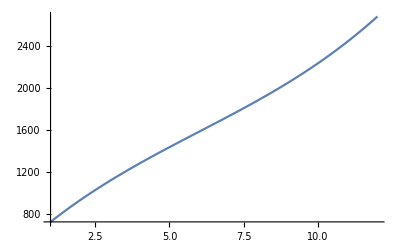

Question 7

Cost function is TC(Q)=1000+120 Q-60 Q^2+10 Q^3

Q_min^AVC=3

Q_min^MC=2

Q_min^ATC=5

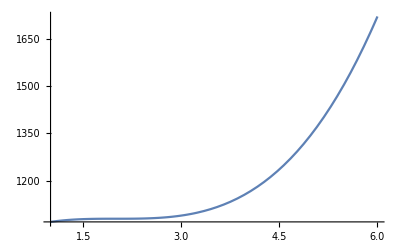

Question 8

Cost function is TC(Q)=64+24 Q-12 Q^2+2 Q^3

Q_min^AVC=3

Q_min^MC=2

Q_min^ATC=4

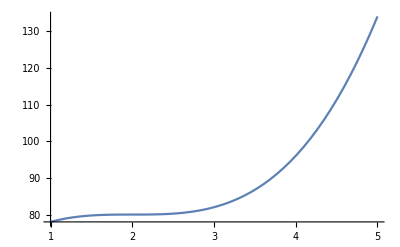

Question 9

Cost function is TC(Q)=96800+2612 Q-240 Q^2+10 Q^3

Q_min^AVC=12

Q_min^MC=8

Q_min^ATC=22

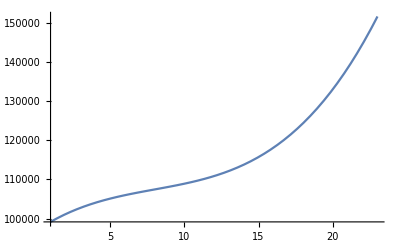

Question 10

Cost function is TC(Q)=10752+700 Q-54 Q^2+3 Q^3

Q_min^AVC=9

Q_min^MC=6

Q_min^ATC=16

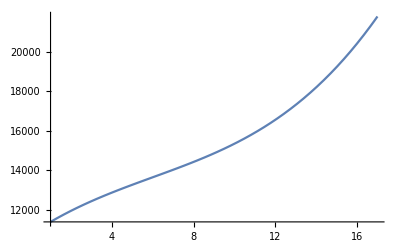

```mathematica
n=10; (*number of questions needed*)
generate[n_]:=Module[{QAVCmin,QMCmin,QATCmin},
SeedRandom[n];
k=RandomInteger[{1,5}];
δ=RandomInteger[{1,10}];
γ=-6*δ*k;
β=RandomInteger[{γ^2/(3δ),(k*γ^2)/(3δ)}];
QAVCmin=-γ/(2δ);
QMCmin=-γ/(3δ);
QATCmin=RandomInteger[{QAVCmin+1,2*QAVCmin}];
α=γ*QATCmin^2+2δ*QATCmin^3;

Print["Question ",i];
Print["Cost function is TC(Q)=", α+β*Q+γ*Q^2+δ*Q^3];
Print["Q_min^AVC=",QAVCmin];
Print["Q_min^MC=",QMCmin];
Print["Q_min^ATC=",QATCmin];
Print[Plot[(α+β*Q+γ*Q^2+δ*Q^3),{Q,1,QATCmin+1}]];
{}
];

Table[generate[i],{i,1,n}]//TableForm;
(*CODE ABOVE*)
(************)
(*OUTPUT BELOW*)
```